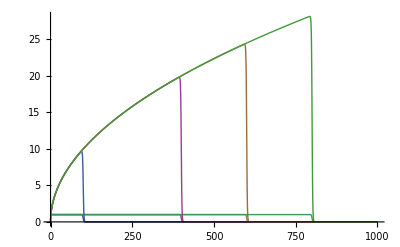

```mathematica
Clear[f]
f[x_, y_, nu_] = x^(nu-1)/(E^(x - y) + 1) ;

Manipulate[
Plot[f[x, y, nu],
 {x, 0, y},
PlotRange -> Full
],
{{nu, 1}, -1/2, 9/2, 1/2},
{{y, 100}, 10, 100000}
]

Module[{a, b},
a[x_, nu_] = Map[ 
f[x, #, nu]
&, { 100, 400, 600, 800}] ;
b[x_] = Flatten[Map[ a[x, #]&, {1, 3/2(*, 2, 5/2*)}]] ;

Plot[
Evaluate[b[x]]
,
 {x, 0, 1000},
PlotRange -> Full

]]
```

```mathematica
(*Clear[f, y, a, nu]
f[x_, y_, nu_] = x^(nu-1)/(E^(y -x) + 1) 
Integrate[ f[x, y, nu], {x, 0, y}]
*)
(*Manipulate[
Plot[
Integrate[
f[a, y, nu],
 {a, 0, 100},
PlotRange -> Full
],
{y, 1, 1000},
{{nu, 1}, -1/2, 9/2, 1/2}
]*)
```

```mathematica
Clear[j, i]
$Assumptions = j ∈ Integers && j > 0
i = Integrate[a^j/(E^a + 1), {a, 0, Infinity}]
i // TraditionalForm
```

j∈Integers&&j>0

2^-j (-1+2^j) j! Zeta[1+j]

2^-j (2^j-1) j! j+1

```mathematica
Product[ (nu-k), {k, 1, j}]
```

```mathematica
((-j+nu) Pochhammer[1-j+nu,j])/nu
```

```mathematica
(*((-j+nu) Gamma[1-j+nu +j])/(nu Gamma[1 -j + nu])   -> Gamma[nu]/Gamma[nu- j]*)
```

```mathematica
Clear[c]
c[j_] = 2 (1 - 2^(-j)) Zeta[j+1]
Map[ c[#] &, {1, 3, 5, 7}]
```

2 (1-2^-j) Zeta[1+j]

{π^2/6,(7 π^4)/360,(31 π^6)/15120,(127 π^8)/604800}

```mathematica
c[j] // TraditionalForm
```

2 (1-2^-j) j+1

```mathematica
Clear[i]
$Assumptions = alpha > 0 ;
 
i = (1/Gamma[nu])Integrate[x^(nu-1)/(alpha + x), {x, 0, Infinity}] ;

i /. nu -> ν /. alpha -> α// FullSimplify //  TraditionalForm
```

ConditionalExpression[(π α^(ν-1) csc(π ν))/ν,0<Re(ν)<1]

```mathematica
Map[ Zeta[#] &, {3/2, 2, 5/2, 3}] // N
```

{2.61238,1.64493,1.34149,1.20206}